Dataset[<>]

x_1&&x_2&&c_1&&c_2&&d_1&&d_2&&d_3&&d_4&&d_5&&d_6&&d_7&&d_8&&d_9&&d_10&&x_5&&x_6&&(g_1||g_2)&&(h_1||h_2)&&(i_1||i_2)

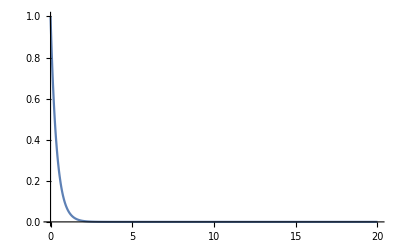

0.37037

```mathematica
(* Считаем для сервера RH1288 *)
removeAll:=Remove[Evaluate[$Context<>"*"]];

removeAll
Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"HDD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}]

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{Array[{Subscript[x, #],ExponentialDistribution[0.3]}&,9], Array[{Subscript[c, #],ExponentialDistribution[0.3]}&,2], Array[{Subscript[d, #],ExponentialDistribution[0.5]}&,10], Array[{Subscript[g, #],ExponentialDistribution[0.05]}&,2],Array[{Subscript[h, #],ExponentialDistribution[0.05]}&,2],Array[{Subscript[i, #],ExponentialDistribution[0.05]}&,2]} ,1];
bexpr=And @@Array[Subscript[x, #]&,9];
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (*CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (*RAM *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9]
ℛ=ReliabilityDistribution[bexpr,dists];
Plot[SurvivalFunction[ℛ,t]//Evaluate,{t,0,20},PlotRange->All]
Mean[ℛ]//N
```

```mathematica
(* см. ref/ReliabilityDistribution Applications

A vacuum system in a small electron accelerator contains 20 vacuum bulbs arranged in a circle.The vacuum system fails if at least three adjacent vacuum bulbs fail: *)
n=20;k=3;
bexpr=And@@Map[Or@@#&,Partition[Array[Subscript[x, #]&,n],k,1,{-1,-1}]]
```

```mathematica
ExponentialDistribution[λ];
With[{n=5,m=2},Binomial[n+m-1,m]];
(* Резервирование с дробной кратностью *)
pSystem[n_,m_,t_]:=∑_(i=0)^m (Binomial[n,i](1-PDF[ExponentialDistribution[λ], t])^i PDF[ExponentialDistribution[λ],t]^(n-i))
```

```mathematica
ExponentialDistribution[λ]
```

ExponentialDistribution[λ]

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
pSystem[2,4,t] /. {λ->0.05} //N
pSystem[2,4,1] /. {λ->0.05} //N
```

(1.-1. (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}]))^2+2. (1.-1. (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])) (Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])+(Piecewise[{{0.05 2.71828^(-0.05 t), t≥0.}, {0., True}}])^2

1.

1/λ_1+1/λ_2-1/(λ_1+λ_2)

Piecewise[{{1, t<0}, {ⅇ^(-t (λ_1+λ_2)) (-1+ⅇ^(t λ_1)+ⅇ^(t λ_2)), True}}]

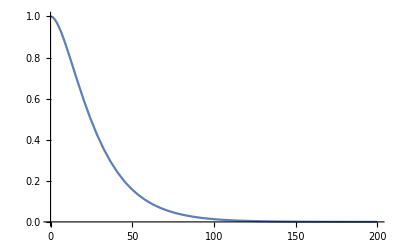

```mathematica
ℛ=ReliabilityDistribution[x||y||(x&&y),{{x,ExponentialDistribution[Subscript[λ, 1]]},{y,ExponentialDistribution[Subscript[λ, 2]]}}];
Mean[ℛ]
SurvivalFunction[ℛ,t]//Simplify
Plot[SurvivalFunction[ℛ,t] /. {Subscript[λ, 1]->0.05,Subscript[λ, 2]->0.05},{t,0,200},PlotRange->All]
```

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

```mathematica
BooleanCountingFunction[2,4][a,b,c, d]
BooleanConvert[%]
```

BooleanCountingFunction[2,4][a,b,c,d]

(!a&&!b)||(!a&&!c)||(!a&&!d)||(!b&&!c)||(!b&&!d)||(!c&&!d)

```mathematica
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[Subscript[λ, i]],{i,3}];
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[λ],{i,3}];
bcf=BooleanCountingFunction[{3,4},4][a,b,c,d]
UnateQ[bcf]
BooleanConvert[bcf]
(*ℛ=ReliabilityDistribution[x ||y,{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}]*)
ℛ=ReliabilityDistribution[BooleanCountingFunction[{2,3},3][x,y,z],{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}]

λ=0.05
SurvivalFunction[ℛ,t]//Simplify
Mean[ℛ]
N[%]
Probability[t<0.5,t\[Distributed]ℛ]
```

```mathematica
Mean[ℛ] // N
```

BooleanCountingFunction::bspec: BooleanCountingFunction[{2.,3.},3.] is not a valid BooleanCountingFunction specification.

ReliabilityDistribution::vundef: The variable BooleanCountingFunction[{2.,3.},3.][x1,x2,x3] has no associated distribution.

Mean[ReliabilityDistribution[BooleanCountingFunction[{2.,3.},3.][x1,x2,x3],{{x1,ExponentialDistribution[0.05]},{x2,ExponentialDistribution[0.05]},{x3,ExponentialDistribution[0.05]}}]]

```mathematica
{Subscript[𝒟, 1],Subscript[𝒟, 2],Subscript[𝒟, 3]}=Table[ExponentialDistribution[Subscript[λ, i]],{i,3}]
Subscript[𝒟, 1]
ℛ=ReliabilityDistribution[BooleanConsecutiveFunction[2,3][x,y,z],{{x,Subscript[𝒟, 1]},{y,Subscript[𝒟, 2]},{z,Subscript[𝒟, 3]}}];
SurvivalFunction[ℛ,t]//Simplify
```

{ExponentialDistribution[λ_1],ExponentialDistribution[λ_2],ExponentialDistribution[λ_3]}

ExponentialDistribution[λ_1]

Piecewise[{{1, t<0}, {ⅇ^(-t (λ_1+λ_2+λ_3)) (-1+ⅇ^(t λ_1)+ⅇ^(t λ_3)), True}}]